{1,2}

{1.44853,1.44581}

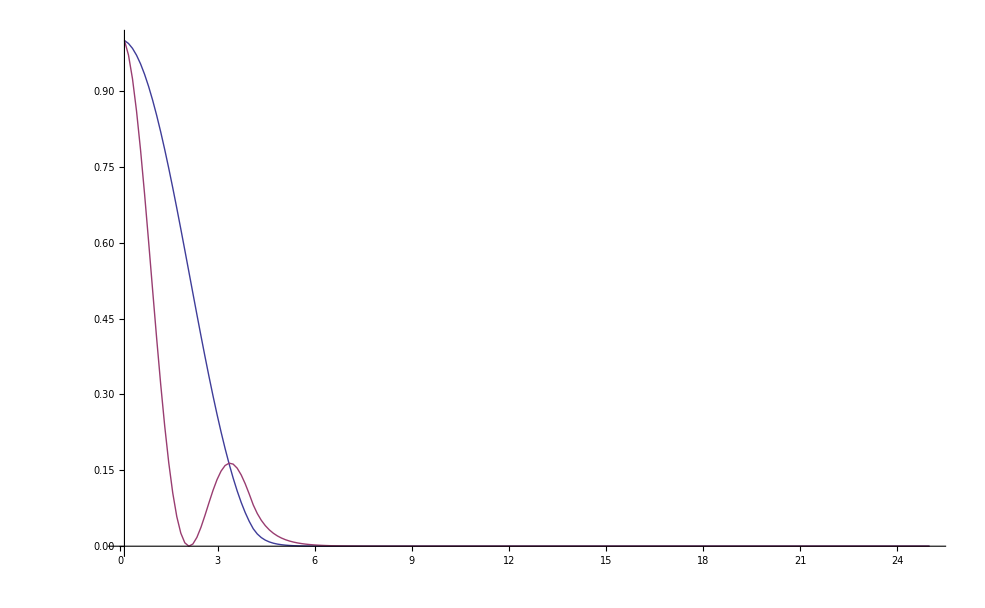

```mathematica
Clear["Global`*"]

NN=201;
rMax=25;
h=rMax/NN;

nMat=1.444;
k0=2Pi/1.55;
l=0;

(*1*)
RIP=Array[(0.0036HeavisideTheta[8.2/2-h#]+1)nMat&,NN];

(*2*)
D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{3/2,-2,1/2},NN];

(*3*)
D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{1,-4,5,-2},NN];

(*4*)
DivByr=Array[1/h/#&,NN];

{β,Modes}=Eigensystem[D2/h^2+1/h D1 DivByr-l^2DivByr^2 IdentityMatrix[NN]+k0^2 RIP^2 IdentityMatrix[NN]];
β=Sqrt[β];
Modes=Modes/(Max/@Abs[Modes]);

(*Я*)
TrueModes=Select[Range[NN],Re[β/k0][[#]]>nMat&]
Re[β/k0][[%]]
ListPlot[Modes[[%%]]^2,PlotRange->All,DataRange->{h,rMax},Joined->True]
```

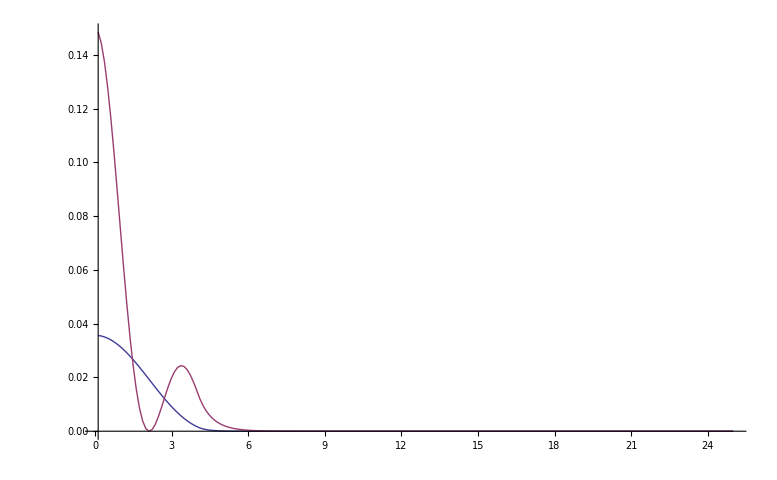

```mathematica
ListPlot[Abs[Modes[[TrueModes]]]^2,PlotRange->All,DataRange->{h,rMax},Joined->True]
```

Домашнее задание
1) Написать функцию, которая на вход получает двумерный массив из коэффициентов Селмейера произвольной длины {{a1,l1},{a2,l2},...,{an,ln}} и длину волны λ, на выходе функция выдает показатель преломления. Возможно для этих целей пригодится оператор Map /@. Построить кривую показателя преломления и построить кривую материальной дисперсии для кварцевого стекла в зависимости от длины волны. 
2) Численно решить трансцендентное характеристическое уравнение для ППП - ступеньки на примере SMF28. Найти эффективный групповой показатель преломления, построить график моды.
3) Импортировать измеренный ППП из файла SMF28 и симметризовать. Составить матрицу разностного уравнения 4 степени точности. Найти моды такого волокна. Пронормировать моды по 1) ∫|Ψ|^2ds = 1, 2) мощности P = 1Вт. Не забыть Якобиан, интеграл заменить на сумму (метод прямоугольников). Построить график интенсивности моды.